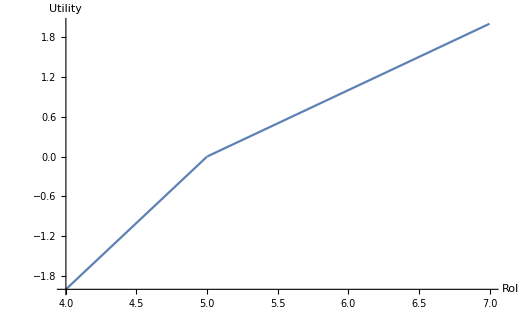

```mathematica
Plot[Max[x-5,0]-2Max[5-x,0],{x,4,7},AxesLabel->{"RoI","Utility"},AxesOrigin->{4,-2},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14}]
```

```mathematica
stocks={"MSFT","AAPL","GOOG"};
y=2015;
```

```mathematica
ans=solveObjective[{"MSFT","AAPL","GOOG"},2015]
```

{-0.462577,0.0813624,0.118456,0.0476892,0.0255442,0.145512,-0.860971}

```mathematica
q=ans
```

{-0.462577,0.0813624,0.118456,0.0476892,0.0255442,0.145512,-0.860971}

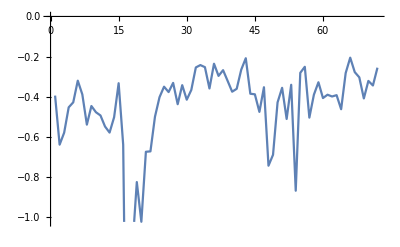

```mathematica
ListLinePlot[xs.ans]
```

```mathematica
rangeVars[q,7]
```

{q$1,q$2,q$3,q$4,q$5,q$6,q$7}

```mathematica
ans=%
```

{q$1→-0.462577,q$2→0.0813624,q$3→0.118456,q$4→0.0476892,q$5→0.0255442,q$6→0.145512,q$7→-0.860971}

```mathematica
rangeVars[q,7]/.ans
```

{-0.462577,0.0813624,0.118456,0.0476892,0.0255442,0.145512,-0.860971}

```mathematica
xs=adjustFeaturesMatrix[x[y]/@stocks];
rs=Flatten[r[y]/@stocks,1];
```

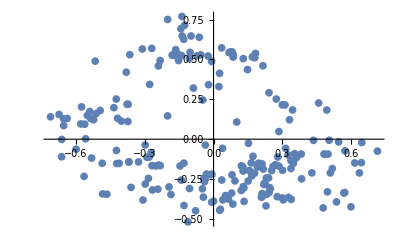

```mathematica
ListPlot@
Flatten[
Map[Function[xStock,
(*#[[3;;4]]&/@xStock]*)
Transpose@MapThread[Standardize[{##},Mean,Function[3StandardDeviation[##]]]&,#[[3;;4]]&/@xStock]],
xs],
1]
```

```mathematica
{a,b,c}≥{1,2,3}
```

{4,b,c}≥{1,2,3}

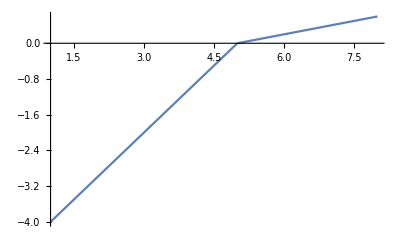

```mathematica
U[p_]:=0.2 (p-5)+Min[(1-0.2)*(p-5),0];
Plot[U[p],{p,1,8}]
```

```mathematica
stocks={"AAPL"};
y=2015;
```

```mathematica
solveObjective[stocks,y]
```

{-0.0281717,0.0000942056,0.0140221,0.0384223,0.0010725,-0.0246407,0.00887866,-0.00381048,-0.0271403,-0.00777011,0.0257572,0.00763432,0.0260156,0.00516014,0.00106206,-0.0350132,0.0565328,0.0311335,-0.0146341,0.0125469,0.000168664,0.00766959,0.0110841,-0.00842088,0.00664256,0.0192115,0.0234388,0.0126521,0.00490274,0.00590179,0.00696237,-0.00209758,0.00817439,0.027027,-0.0062406,-0.0255732,0.0126563,-0.0150283,0.00490417,0.00209156,-0.00633898,-0.0165706,0.00150305,0.0042654,-0.0206859,-0.0182315,0.0180792,-0.00691041,0.0110041,0.0167267,0.0112563,-0.0075504,-0.012549,0.0104051,-0.00408773,-0.0261268,0.00697034,-0.00796845,0.0253144,-0.0153517,-0.0014466,0.00861167,0.0161985,-0.0105222,-0.00325371,0.00764331,0.00426675,-0.00196696,-0.00433583,0.00380048,-0.00481148,-0.0112547,0.0228457}

```mathematica
Times[a,b,c]
```

a b c

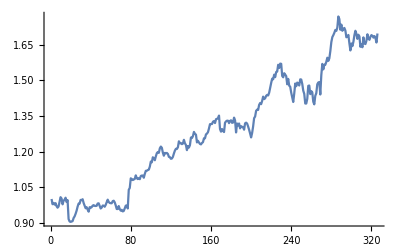

```mathematica
ListLinePlot[rawReturns["AAPL",2014]]
```

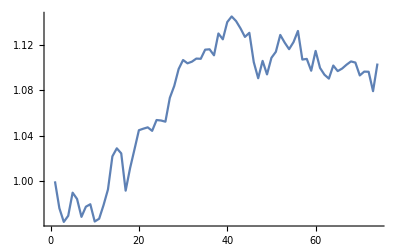

```mathematica
ListLinePlot[rawReturns[{"AAPL","GOOGL"},2015]]
```

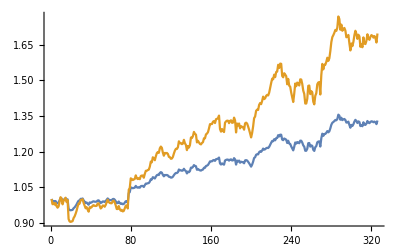

```mathematica
ListLinePlot[{rawReturns[{"AAPL"},2014,{0.5,0.5}],rawReturns["AAPL",2014]}]
```

```mathematica
stocks={"AAPL"};
y=2015;
```

```mathematica
solveObjective[stocks,y]
```

>>  
Calling SDPT3 4.0: 155 variables, 74 equality constraints
------------------------------------------------------------

 num. of constraints = 74
 dim. of linear var  = 148
 dim. of free   var  =  7 *** convert ublk to lblk
*******************************************************************
   SDPT3: Infeasible path-following algorithms
*******************************************************************
 version  predcorr  gam  expon  scale_data
    NT      1      0.000   1        0    
it pstep dstep pinfeas dinfeas  gap      prim-obj      dual-obj    cputime
-------------------------------------------------------------------
 0|0.000|0.000|3.3e-03|1.6e+01|2.5e+04| 9.002489e+02  0.000000e+00| 0:0:00| chol  1  1 
 1|1.000|0.971|3.2e-06|5.5e-01|1.5e+03| 8.155585e+02  1.342449e-02| 0:0:00| chol  1  1 
 2|0.993|0.468|2.7e-06|3.0e-01|6.4e+02| 4.033384e+02  1.328559e-02| 0:0:00| chol  1  1 
 3|0.888|0.535|2.1e-06|1.4e-01|2.9e+02| 1.908799e+02  1.228593e-02| 0:0:00| chol  1  1 
 4|0.435|0.283|2.3e-06|1.0e-01|2.2e+02| 1.309598e+02  1.167470e-02| 0:0:00| chol  1  1 
 5|1.000|0.551|3.4e-07|4.5e-02|1.4e+02| 8.264861e+01  1.097780e-02| 0:0:00| chol  1  1 
 6|1.000|0.670|1.7e-07|1.5e-02|6.6e+01| 4.411851e+01  1.033070e-02| 0:0:00| chol  1  1 
 7|1.000|0.519|7.9e-08|7.1e-03|2.8e+01| 1.959968e+01  1.007692e-02| 0:0:00| chol  1  1 
 8|0.989|0.384|4.3e-08|4.4e-03|1.6e+01| 1.278230e+01  9.931736e-03| 0:0:00| chol  1  1 
 9|1.000|0.480|4.6e-09|2.3e-03|5.7e+00| 4.863129e+00  9.839697e-03| 0:0:00| chol  1  1 
10|1.000|0.695|5.8e-10|7.0e-04|1.1e+00| 1.067393e+00  9.773091e-03| 0:0:00| chol  1  1 
11|0.939|0.448|3.6e-11|3.8e-04|1.5e-01| 1.502784e-01  9.797787e-03| 0:0:00| chol  1  1 
12|1.000|0.742|2.1e-11|9.9e-05|2.4e-02| 3.287641e-02  1.005629e-02| 0:0:00| chol  1  1 
13|1.000|0.603|3.9e-11|3.9e-05|1.2e-02| 2.315748e-02  1.117506e-02| 0:0:00| chol  1  1 
14|1.000|0.274|3.5e-11|3.1e-05|7.7e-03| 1.912998e-02  1.161907e-02| 0:0:00| chol  1  1 
15|1.000|0.673|5.0e-12|1.3e-05|4.4e-03| 1.690453e-02  1.260826e-02| 0:0:00| chol  1  1 
16|1.000|0.867|7.1e-13|5.4e-06|2.2e-03| 1.525804e-02  1.309793e-02| 0:0:00| chol  1  1 
17|1.000|0.624|6.8e-13|2.7e-06|1.1e-03| 1.445518e-02  1.340445e-02| 0:0:00| chol  1  1 
18|1.000|0.892|1.6e-13|1.3e-06|5.0e-04| 1.414187e-02  1.364425e-02| 0:0:00| chol  1  1 
19|0.918|0.926|1.7e-13|6.1e-07|1.1e-04| 1.390592e-02  1.379500e-02| 0:0:00| chol  1  1 
20|0.950|0.940|3.1e-13|1.4e-07|3.7e-05| 1.386010e-02  1.382351e-02| 0:0:00| chol  1  1 
21|1.000|0.984|1.5e-13|4.4e-08|1.8e-06| 1.384091e-02  1.383918e-02| 0:0:00| chol  1  1 
22|1.000|0.989|7.9e-15|2.1e-09|3.3e-08| 1.384011e-02  1.384008e-02| 0:0:00| chol  1  1 
23|1.000|0.989|6.8e-15|4.0e-11|5.8e-10| 1.384010e-02  1.384010e-02| 0:0:00|
  stop: max(relative gap, infeasibilities) < 1.49e-08
-------------------------------------------------------------------
 number of iterations   = 23
 primal objective value =  1.38401016e-02
 dual   objective value =  1.38401011e-02
 gap := trace(XZ)       = 5.76e-10
 relative gap           = 5.60e-10
 actual relative gap    = 5.33e-10
 rel. primal infeas (scaled problem)   = 6.80e-15
 rel. dual     "        "       "      = 3.98e-11
 rel. primal infeas (unscaled problem) = 0.00e+00
 rel. dual     "        "       "      = 0.00e+00
 norm(X), norm(y), norm(Z) = 1.2e-01, 5.9e+00, 8.4e+00
 norm(A), norm(b), norm(C) = 1.3e+01, 1.0e+00, 9.6e+00
 Total CPU time (secs)  = 0.17  
 CPU time per iteration = 0.01  
 termination code       =  0
 DIMACS: 6.8e-15  0.0e+00  1.9e-10  0.0e+00  5.3e-10  5.6e-10
-------------------------------------------------------------------
 
------------------------------------------------------------
Status: Solved
Optimal value (cvx_optval): -0.0208853

{0.0388709,0.0340096,0.0551056,-0.0819132,-0.000809325,0.0543623,-0.00114235}

```mathematica
trainingStocks={"MSFT","GOOGL","YHOO","AMZN"};
trainingYears=2005;
testStock="AAPL";
testYear=2014;
```

```mathematica
{ϕ,A,b}=Φ[x[trainingYears]/@trainingStocks];
```

Calling financial feeds

Calling financial feeds

Calling financial feeds

«1 more identical outputs»

```mathematica
rs=Flatten[r[trainingYears]/@trainingStocks,1];
```

Calling returns values for MSFT

Calling returns values for GOOGL

Calling returns values for YHOO

Calling returns values for AMZN

```mathematica
q=Last@cvxSolve[ϕ,rs];
```

>>  
Calling SDPT3 4.0: 20735 variables, 10364 equality constraints
------------------------------------------------------------

 num. of constraints = 10364
 dim. of linear var  = 20728
 dim. of free   var  =  7 *** convert ublk to lblk
 number of dense column in A = 14
*******************************************************************
   SDPT3: Infeasible path-following algorithms
*******************************************************************
 version  predcorr  gam  expon  scale_data
    NT      1      0.000   1        0    
it pstep dstep pinfeas dinfeas  gap      prim-obj      dual-obj    cputime
-------------------------------------------------------------------
 0|0.000|0.000|6.0e-07|2.0e+02|4.3e+08| 1.492128e+06  0.000000e+00| 0:0:00| spchol  1  1 
 1|1.000|0.934|3.7e-05|1.4e+01|3.0e+07| 1.475436e+06  0.000000e+00| 0:0:00| spchol  1  1 
 2|1.000|0.043|1.9e-04|1.3e+01|4.7e+07| 2.382208e+06  0.000000e+00| 0:0:00| spchol  1  1 
 3|1.000|0.949|6.5e-06|7.8e-01|4.5e+06| 2.130252e+06  0.000000e+00| 0:0:00| spchol  1  1 
 4|1.000|0.953|3.8e-06|9.6e-02|7.2e+05| 6.327077e+05  0.000000e+00| 0:0:00| spchol  1  1 
 5|0.985|0.442|6.4e-08|6.7e-02|6.9e+04| 6.325770e+04  0.000000e+00| 0:0:00| spchol  1  1 
 6|0.989|0.836|1.9e-09|1.9e-02|2.9e+03| 2.778015e+03  0.000000e+00| 0:0:00| spchol  2  1 
 7|0.969|0.986|1.8e-08|1.2e-03|1.2e+02| 1.173959e+02  0.000000e+00| 0:0:00| spchol  2  2 
 8|0.989|1.000|2.0e-10|9.4e-05|1.3e+00| 1.297038e+00  0.000000e+00| 0:0:00| spchol  2  2 
 9|0.989|1.000|2.4e-12|9.4e-06|1.4e-02| 1.424383e-02  0.000000e+00| 0:0:00| spchol  3  2 
10|0.998|1.000|1.0e-11|9.4e-07|1.8e-04| 1.824788e-04  0.000000e+00| 0:0:00| spchol * 5 * 4 
11|0.999|1.000|4.9e-13|9.4e-08|2.0e-06| 2.035774e-06  0.000000e+00| 0:0:01| spchol 21 12 
  stop: primal infeas has deteriorated too much, 1.3e-02
12|0.998|0.444|4.9e-13|9.4e-08|2.0e-06| 2.035774e-06  0.000000e+00| 0:0:01|
-------------------------------------------------------------------
 number of iterations   = 12
 primal objective value =  2.03577354e-06
 dual   objective value =  0.00000000e+00
 gap := trace(XZ)       = 2.04e-06
 relative gap           = 2.04e-06
 actual relative gap    = 2.04e-06
 rel. primal infeas (scaled problem)   = 4.88e-13
 rel. dual     "        "       "      = 9.37e-08
 rel. primal infeas (unscaled problem) = 0.00e+00
 rel. dual     "        "       "      = 0.00e+00
 norm(X), norm(y), norm(Z) = 2.9e-08, 5.1e+01, 7.2e+01
 norm(A), norm(b), norm(C) = 1.5e+02, 1.0e+00, 1.0e+02
 Total CPU time (secs)  = 0.61  
 CPU time per iteration = 0.05  
 termination code       = -7
 DIMACS: 4.9e-13  0.0e+00  1.9e-06  0.0e+00  2.0e-06  2.0e-06
-------------------------------------------------------------------
 
------------------------------------------------------------
Status: Inaccurate/Solved
Optimal value (cvx_optval): -2.03577e-06

```mathematica
q
```

{1.55996×10^-9,-2.87452×10^-10,4.19348×10^-10,-1.39826×10^-10,-1.40852×10^-10,-1.3257×10^-10,-1.43223×10^-10}

```mathematica
testingXs=x[testYear][testStock];
```

Calling financial features feeds for AAPL

```mathematica
testingΦ=Φ[testingXs,A,b];
```

```mathematica
p=testingΦ.q;
```

```mathematica
testReturns=r[testYear][testStock];
```

Calling returns values for AAPL

```mathematica
actualReturns=testReturns*p+Rf*(1-p);
```

Calling returns values for AAPL

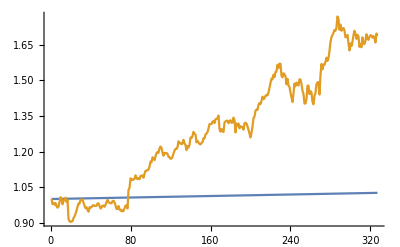

```mathematica
ListLinePlot[{FoldList[Times,1,1+actualReturns],rawReturns[testStock,testYear]}]
```

```mathematica
Length[rawReturns[testStock,testYear]]
```

Calling returns values for AAPL

327

```mathematica
Length[FoldList[Times,1,1+actualReturns]]
```

327

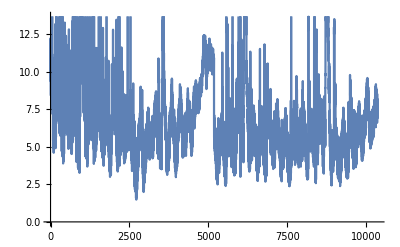

```mathematica
ListLinePlot[Norm/@ϕ]
```

```mathematica
testModel[trainingStocks,trainingYears,testStock,testYear]
```

Calling financial features feeds for MSFT

Calling financial features feeds for GOOGL

Calling financial features feeds for YHOO

Calling financial features feeds for AMZN

Set::shape: Lists {Φ$95812, A$95812, b$95812} and Φ$95812[{{{1., 1., 0.0826372, 0.134333, 6.50029×10^7}, {2., 1., 0.0810002, 0.115019, 1.09442×10^8}, {3., 1., 0.0759875, 0.114432, 7.24635×10^7}, « 46 », {2., 11., 0.0938117, 0.0994275, 7.14694×10^7}, « 2541 »}, {« 1 »}, {« 1 »}, {« 1 », « 49 », « 2541 »}}] are not the same shape.

Calling returns values for MSFT

Calling returns values for GOOGL

$Aborted[]

Calling returns values for YHOO.

Calling returns values for AMZN

Calling financial features feeds for AAPL

Calling returns values for AAPL

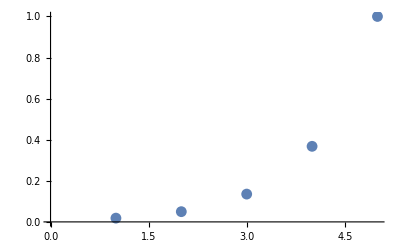

```mathematica
ListPlot[s[0][Range@5]]
```

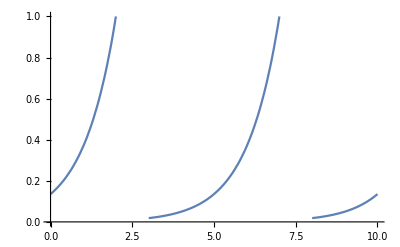

1.

```mathematica
s[d_]:=Function[x,
Exp[1(Mod[x-d,5,1]-5)],
{Listable}];

Plot[s[2][x],{x,0,10},PlotRange->{0,1}]
s[5][5.]
```

```mathematica
Mod[6,5,1]
```

1

```mathematica
Mod[7,5,1]
```

2

```mathematica
dayFeature[Range[5]]
```

Function[x$,Exp[μ_s (Mod[x$-{1,2,3,4,5},5,1]-5)],{Listable}]

```mathematica
xs=x[2015]["AAPL"];
```

Calling financial features feeds for AAPL

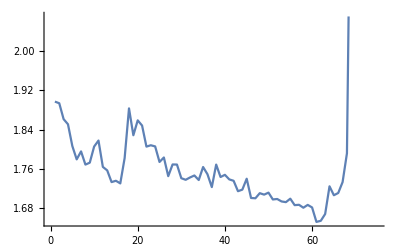

```mathematica
ListLinePlot[Norm/@First[Φ[{xs}]]]
```

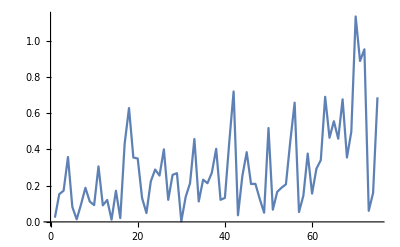

```mathematica
ListLinePlot[Norm/@(Transpose@Rest@Transpose@First[Φ[{xs}]])]
```

```mathematica
Most
```

```mathematica
Dimensions[xs]
```

{75,61}

```mathematica
Dimensions[scaleMatrix[xs]]
```

{75,75}

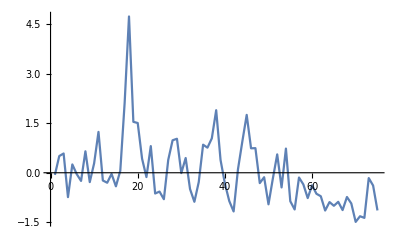

```mathematica
ListLinePlot[(Norm/@xs-Mean[Norm/@xs])/StandardDeviation[Norm/@xs]]
```

```mathematica
(Norm/@xs-Mean[Norm/@xs])/(1StandardDeviation[Norm/@xs])
```

{-0.0644287,0.505336,0.583061,-0.737946,0.252305,-0.0389817,-0.24716,0.649638,-0.282855,0.285701,1.23691,-0.234352,-0.30243,-0.0339992,-0.41098,0.0595108,2.11388,4.73152,1.54147,1.50594,0.425822,-0.130702,0.806866,-0.627895,-0.570008,-0.800477,0.388256,0.982311,1.02924,-0.00953418,0.447074,-0.491867,-0.879013,-0.283277,0.849255,0.759478,1.04144,1.89374,0.38858,-0.32707,-0.855674,-1.1719,0.105896,0.945305,1.75188,0.740376,0.744613,-0.313393,-0.135248,-0.95553,-0.176599,0.556004,-0.444675,0.732072,-0.861156,-1.11143,-0.144097,-0.354003,-0.766725,-0.378335,-0.635896,-0.71144,-1.14342,-0.887672,-0.999852,-0.880721,-1.12985,-0.733725,-0.930293,-1.4877,-1.31677,-1.3658,-0.161132,-0.386834,-1.14063}

```mathematica
Normal@scaleMatrix[magic[5],k]//MatrixForm
```

(0.0526316 | 0. | 0. | 0. | 0.
0. | 0.0526316 | 0. | 0. | 0.
0. | 0. | 0.0416667 | 0. | 0.
0. | 0. | 0. | 0.0526316 | 0.
0. | 0. | 0. | 0. | 0.0526316)

```mathematica
magic[5]//MatrixForm
```

(17. | 24. | 1. | 8. | 15.
23. | 5. | 7. | 14. | 16.
4. | 6. | 13. | 20. | 22.
10. | 12. | 19. | 21. | 3.
11. | 18. | 25. | 2. | 9.)

```mathematica
Norm/@First[Φ[{magic[5]}]]
```

{1.30761,1.24278,1.31157,1.24278,1.30761}

```mathematica
Mean[magic[5]]
```

{13,13,13,13,13}

```mathematica
magic[5]-ConstantArray[Mean[magic[5]],5]//MatrixForm
```

(4 | 11 | -12 | -5 | 2
10 | -8 | -6 | 1 | 3
-9 | -7 | 0 | 7 | 9
-3 | -1 | 6 | 8 | -10
-2 | 5 | 12 | -11 | -4)

```mathematica
Mean[Range@5]
```

3

```mathematica
(Range@5-3)/2
```

{-1,-1/2,0,1/2,1}

```mathematica
Norm[{1,1}]
```

√2